# IGraph/M

## use igraph from Mathematica

This notebook can (and should) be opened using the command IGDocumentation[]. When opened like this, it cannot be saved, so feel free to re-evaluate cells and experiment.

The documentation is currently incomplete. Contributions are welcome!

## Basic usage

The package can be loaded using

```mathematica
<<IGraphM`
```

Evaluate IGDocumentation[] to get started.

The list of included functions is below. Notice that their names always have the IG prefix. Click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

Or just type a question mark followed by the symbol’s name:

```mathematica
?IGVersion
```

IGVersion[] returns the IGraph/M version along with the version of the igraph library in use.

```mathematica
IGVersion[]
```

IGraph/M 0.1.3dev
igraph 0.8.0-pre+6af4443 (Oct  7 2015)
Mac OS X x86 (64-bit)

IGraph/M functions work directly with Mathematica’s built-in Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples. Let us first generate a graph using the built-in functions of Mathematica.

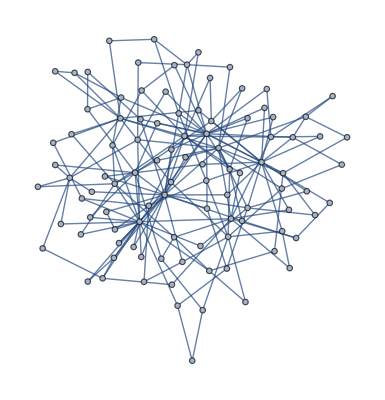

```mathematica
SeedRandom[42];
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex using IGraph/M ...

```mathematica
IGBetweenness[g]
```

{1118.26,1058.15,540.601,127.365,1175.53,678.175,206.929,128.576,204.019,535.316,487.858,391.669,0.,135.039,0.,52.5324,104.28,12.2286,75.8798,110.155,68.8282,13.9095,46.4209,99.3299,0.,168.196,213.871,358.855,0.,64.9572,5.12619,102.369,17.978,15.569,95.7266,8.45843,25.4984,13.0274,0.,71.2012,47.2895,32.4444,8.20833,0.,27.0286,10.9357,4.60238,0.,14.7095,24.7944,79.125,7.38301,22.0817,43.9635,11.7135,10.9952,40.8782,11.2429,0.,60.0431,9.36667,32.4529,85.4487,100.431,15.205,93.2876,60.0548,9.2,0.,0.,10.512,9.37438,8.42222,45.7937,3.61667,9.23333,53.3897,11.4012,22.0959,5.24091,10.2647,8.66017,9.97438,11.0429,15.8765,12.7798,0.,30.1744,0.,0.,4.0373,9.7,1.,10.4883,0.,0.,13.7861,13.8594,1.7,2.80952}

... or using Mathematica, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

{1118.26,1058.15,540.601,127.365,1175.53,678.175,206.929,128.576,204.019,535.316,487.858,391.669,0.,135.039,0.,52.5324,104.28,12.2286,75.8798,110.155,68.8282,13.9095,46.4209,99.3299,0.,168.196,213.871,358.855,0.,64.9572,5.12619,102.369,17.978,15.569,95.7266,8.45843,25.4984,13.0274,0.,71.2012,47.2895,32.4444,8.20833,0.,27.0286,10.9357,4.60238,0.,14.7095,24.7944,79.125,7.38301,22.0817,43.9635,11.7135,10.9952,40.8782,11.2429,0.,60.0431,9.36667,32.4529,85.4487,100.431,15.205,93.2876,60.0548,9.2,0.,0.,10.512,9.37438,8.42222,45.7937,3.61667,9.23333,53.3897,11.4012,22.0959,5.24091,10.2647,8.66017,9.97438,11.0429,15.8765,12.7798,0.,30.1744,0.,0.,4.0373,9.7,1.,10.4883,0.,0.,13.7861,13.8594,1.7,2.80952}

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

{1569.,1509.,697.,506.,1510.,948.,173.,0.,106.,827.,663.,379.,0.,318.,0.,360.,0.,0.,83.,129.,1.,0.,227.,582.,0.,91.,236.,213.,0.,60.,0.,334.,1.,53.,549.,0.,0.,0.,0.,10.,0.,0.,0.,0.,68.,68.,17.,357.,27.,16.,80.,0.,0.,0.,437.,0.,0.,0.,52.,22.,0.,0.,62.,139.,93.,187.,1.,7.,0.,0.,0.,16.,0.,69.,10.,98.,0.,1.,4.,21.,0.,0.,0.,0.,0.,0.,0.,43.,0.,0.,98.,0.,0.,0.,0.,0.,0.,63.,25.,4.}

Notice that Mathematica 10.2 does not include functionality to compute weighted betweenness. BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

{1118.26,1058.15,540.601,127.365,1175.53,678.175,206.929,128.576,204.019,535.316,487.858,391.669,0.,135.039,0.,52.5324,104.28,12.2286,75.8798,110.155,68.8282,13.9095,46.4209,99.3299,0.,168.196,213.871,358.855,0.,64.9572,5.12619,102.369,17.978,15.569,95.7266,8.45843,25.4984,13.0274,0.,71.2012,47.2895,32.4444,8.20833,0.,27.0286,10.9357,4.60238,0.,14.7095,24.7944,79.125,7.38301,22.0817,43.9635,11.7135,10.9952,40.8782,11.2429,0.,60.0431,9.36667,32.4529,85.4487,100.431,15.205,93.2876,60.0548,9.2,0.,0.,10.512,9.37438,8.42222,45.7937,3.61667,9.23333,53.3897,11.4012,22.0959,5.24091,10.2647,8.66017,9.97438,11.0429,15.8765,12.7798,0.,30.1744,0.,0.,4.0373,9.7,1.,10.4883,0.,0.,13.7861,13.8594,1.7,2.80952}

Let us delete the minimum feedback edge set to obtain an acyclic graph:

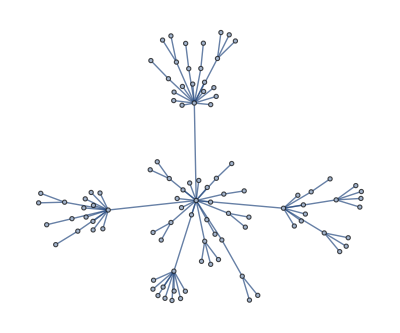

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

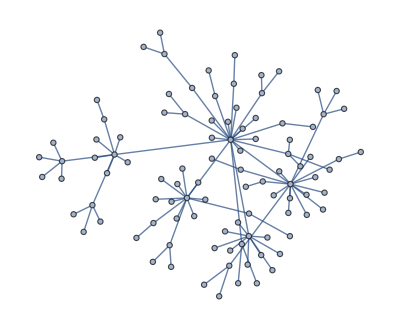
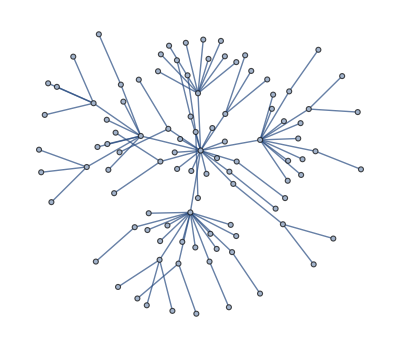
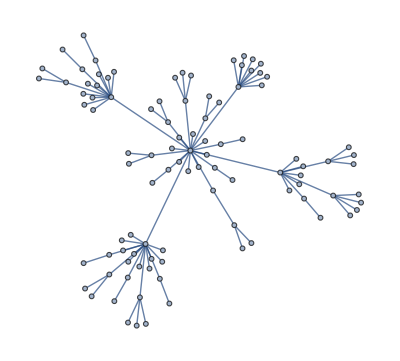

```mathematica
IGSeedRandom[42];
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

{MaxIterations→500,NodeCharge→0.001,NodeMass→30,SpringLength→0,SpringConstant→1,MaxStepMovement→5,Continue→False,Align→True}

Increasing the number of iterations will usually improve the result.

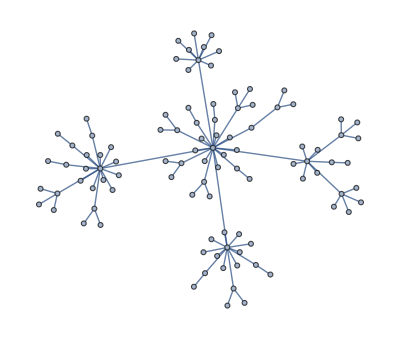

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. The igraph documentation provides article references for most nontrivial algorithms. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not yet be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, GraphStyle, VertexStyle, etc.

```mathematica
IGLCF[{5,-5},7,GraphStyle->"SmallNetwork"]
```

-Graphics-

Many included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

#### IGLCF

```mathematica
?IGLCF
```

IGLCF[shifts, repeats] creates a graph from LCF notation.
IGLCF[shifts, repeats, vertexCount] creates a graph from LCF notation with the number of vertices specified.

IGLCF creates a graph based on LCF notation.

The Möbius–Kantor graph is [5,-5]^8.

```mathematica
IGLCF[{5,-5},8,GraphStyle->"DiagramGreen"]
```

-Graphics-

The Pappus graph is [5,7,-7,7,-7,-5]^3.

```mathematica
IGLCF[{5,7,-7,7,-7,-5},3,GraphStyle->"DiagramBlue"]
```

-Graphics-

#### IGGraphAtlas

```mathematica
?IGGraphAtlas
```

IGGraphAtlas[n] returns graph number n from An Atlas of Graphs by Ronald C. Read and Robin J. Wilson, Oxford University Press, 1998. This function is provided for convenience; if you are looking for a specific named graph, use the builtin GraphData function.

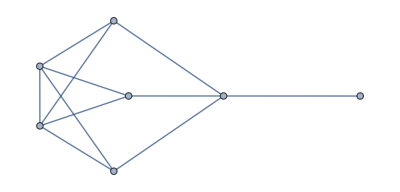

```mathematica
IGGraphAtlas[789]
```

#### IGMakeLattice

```mathematica
?IGMakeLattice
```

IGMakeLattice[{d1, d2, …}] generates a lattice graph of the given dimensions.

IGMakeLattice[{d_1,d_2,…}] creates a lattice graph of the given dimensions. The available options are:

"Radius" controls the size of the neighbourhood within which vertices will be connected.

"Periodic"→True to creates a periodic lattice.

"Mutual"→True inserts directed edges in both directions when DirectedEdges→True is used.

#### IGDegreeSequenceGame

```mathematica
?IGDegreeSequenceGame
```

IGDegreeSequenceGame[degrees] generates an undirected random graph with the given degree sequence. Available Method options: {"VigerLatapy", "SimpleNoMultiple", "Simple"}.
IGDegreeSequenceGame[indegrees, outdegrees] generates a directed random graph with the given in- and out-degree sequences.

IGDegreeSequenceGame takes the following values for its Method option:

"Simple" may generate both self-loops and multiple edges.

"SimpleNoMultiple" avoids self-loops and multiple edges, but it does not guarantee uniform sampling from the space of all graphs with the given degree sequence.

"VigerLatapy" can sample undirected, connected simple graphs uniformly and uses Monte-Carlo methods to randomize the graphs. This generator should be favoured if undirected and connected graphs are to be generated and execution time is not a concern. igraph uses the original implementation of Fabien Viger; see http://www-rp.lip6.fr/~latapy/FV/generation.html and the paper cited on it for the details of the algorithm.

#### IGKRegularGame

```mathematica
?IGKRegularGame
```

IGKRegularGame[n, k] generates a k-regular graph on n vertices, i.e. a graph in which all vertices have degree k.

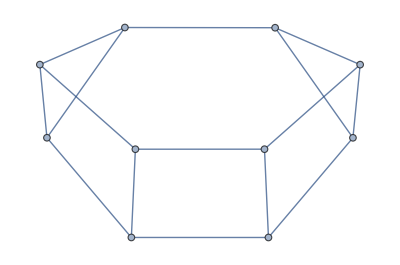

```mathematica
IGKRegularGame[10,3]
```

Not all parameters are valid:

```mathematica
IGKRegularGame[5,3]
```

IGraphM::error: "games.c:931, No simple undirected graph can realize the given degree sequence"

IGraphM::error: "games.c:3874, "

IGraphM::error: "igraph returned with error: Invalid value"

General::stop: Further output of IGraphM :: error will be suppressed during this calculation.

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

```mathematica
IGGraphicalQ[{3,3,3,3,3}]
```

False

#### IGStochasticBlockModelGame

```mathematica
?IGStochasticBlockModelGame
```

IGStochasticBlockModelGame[ratesMatrix, blockSizes] samples from a stochastic block model.

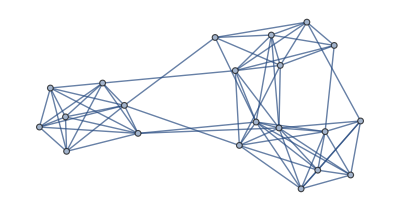

```mathematica
IGStochasticBlockModelGame[({{0.9, 0.1, 0.2}, {0.1, 1, 0.05}, {0.2, 0.05, 0.9}}),{6,7,8}]
```

#### IGForestFireGame

```mathematica
?IGForestFireGame
```

IGForestFireGame[n, fwprob]

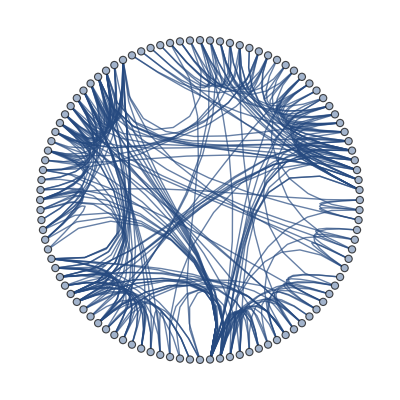

```mathematica
IGForestFireGame[100,0.2,1,2, GraphLayout->{"EdgeLayout"->"HierarchicalEdgeBundling"}]
```

## Structural properties

### Centrality measures

#### Betweenness

```mathematica
?IGBetweenness
```

IGBetweenness[graph] gives a list of betweenness centralities for the vertices of graph. Available Method options: {"Precise", "Fast"}.

```mathematica
?IGBetweennessEstimate
```

IGBetweennessEstimate[graph, cutoff] estimates vertex betweenness by consdering only paths of at most length cutoff. Available Method options: {"Precise", "Fast"}.

Weighted graphs are supported.

Available Method options:

"Precise" is accurate, but slow. This is the default.

"Fast" is fast, but may give incorrect results for large graphs with lots of shortest paths.

```mathematica
g=GridGraph[{30,30}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

{0.262473,18980.5}

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

{0.036103,18980.5}

For this large grid graph, the "Fast" method no longer gives accurate results:

```mathematica
g=GridGraph[{40,40}];
```

```mathematica
Timing[Max@IGBetweenness[g,Method->"Precise"]]
```

{0.924015,45701.7}

```mathematica
Timing[Max@IGBetweenness[g,Method->"Fast"]]
```

{0.114191,78169.7}

#### Closeness

```mathematica
?IGCloseness
```

IGCloseness[graph] gives a list of closeness centralities for the vertices of graph.

```mathematica
?IGClosenessEstimate
```

IGClosenessEstimate[graph, cutoff] estimates closeness centrality by consdering only paths of at most length cutoff.

Weighted graphs are supported.

#### PageRank

```mathematica
?IGPageRank
```

IGPageRank[graph] gives a list of PageRank centralities for the vertices of the graph.
IGPageRank[graph, damping] gives a list of PageRank centralities for the vertices of the graph using damping factor damping.

```mathematica
?IGPersonalizedPageRank
```

IGPersonalizedPageRank[graph, reset] gives a list of personalized PageRank centralities for the vertices of the graph.
IGPersonalizedPageRank[graph, reset, damping] gives a list of personalized PageRank centralities for the vertices of the graph using damping factor damping.

Weighted graphs are supported.

The default damping factor is 0.85.

The following Method options are available:

"PowerIteration", deprectated, not recommended. Takes suboptions "MaxIterations" and "Epsilon".

"Arnoldi" uses ARPACK

"PRPACK" uses PRPACK. It is the default.

#### Eigenvector centrality

```mathematica
?IGEigenvectorCentrality
```

IGEigenvectorCentrality[graph]

#### Kleinberg’s hub and authority scores

```mathematica
?IGHubScore
```

IGHubScore[graph] returns Kleinberg's hub score for each vertex.

```mathematica
?IGAuthorityScore
```

IGAuthorityScore[graph] returns Kleinberg's authority score for each vertex.

#### Burt’s constraint score

```mathematica
?IGConstraintScore
```

IGConstraintScore[graph] returns Burt's constraint score for each vertex.

### Topological sorting and acyclic graphs

IGFeedbackArcSet[] returns a set of edges the removal of which makes the graph acyclic. With "Exact"→True it finds a minimal feedback arc set. With "Exact"→False it finds a feedback arc set (not necessarily minimal) using the heuristic of Eades, Lin and Smyth (1993).

### Chordal graphs

The maximum cardinality search algorithm visits the vertices of the graph in such an order so that every time the vertex with the most already visited neighbors is visited next. The visiting order is animated below:

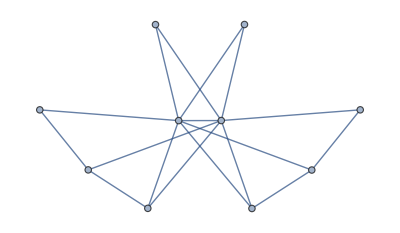
```mathematica
g=-Graphics-;
```

```mathematica
seq=InversePermutation@IGMaximumCardinalitySearch[g]
```

{7,6,2,9,8,4,5,3,10,1}

```mathematica
Table[
HighlightGraph[
Graph[g,VertexLabels->"Name"],
Take[seq,-i]
],
{i,1,10}
]//ListAnimate
```

## Isomorphism

igraph implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality. Most of IGraph/M’s isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. The exceptions are IGIsomorphicQ[] and IGSubisomorphicQ[], which use igraph’s default method for selecting the best option for the current type of graph.

Functions named as …GetIsomorphism will find a single isomorphism. Functions names as …FindIsomorphisms can find multiple isomorphisms. Both return a result in a format compatible with the built-in FindGraphIsomorphism.

```mathematica
?IGIsomorphicQ
```

IGIsomorphicQ[graph1, graph2] tests if graph1 and graph2 are isomorphic.

```mathematica
?IGSubisomorphicQ
```

IGSubisomorphicQ[subgraph, graph] tests if subgraph is contained within graph.

### BLISS

See http://www.tcs.hut.fi/Software/bliss/ and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470920858320

The current implementation only supports undirected graphs.

```mathematica
?IGBliss*
```

Bliss functions take a "SplittingHeuristics" option, which can influence the performance of the method. Possible values are:

"First" – First non-unit cell. Very fast but may result in large search spaces on difficult graphs. Use for large but easy graphs.

"FirstSmallest" – First smallest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstLargest" – First largest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstMaximallyConnected" – First maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstSmallestMaximallyConnected" – First smallest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstLargestMaximallyConnected" – First largest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

Note: The result of the IGBlissCanonicalLabeling, IGBlissCanonicalPermutation and IGBlissanonicalGraph functions depend on the choice of "SplittingHeuristics". See the Bliss documentation for more information.

### VF2

```mathematica
?IGVF2*
```

VF2 supports vertex coloured and edge coloured graphs. Colours can be provided as a pair of integer lists using the "VertexColors" or "EdgeColors" options.

### LAD

See http://liris.cnrs.fr/csolnon/LAD.html and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470934622128

```mathematica
?IGLAD*
```

With the "Induced"→True option LAD will search for induced subgraphs.



```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-]
```

True

```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

False

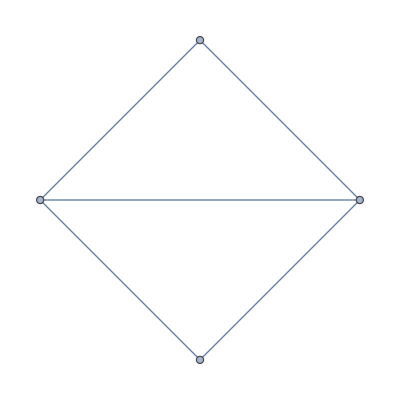
```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

True

## Maximum flow and connectivity

### Cohesive blocks

The following examples are based on the ones in the R/igraph documentation.

This is the network from the Moody-White paper:

J. Moody and D. R. White. Structural cohesion and embeddedness: A hierarchical concept of social groups. American Sociological Review, 68(1):103–127, Feb 2003.

```mathematica
mw=Graph[{"1"<->"2","1"<->"3","1"<->"4","1"<->"5","1"<->"6","2"<->"3","2"<->"4","2"<->"5","2"<->"7","3"<->"4","3"<->"6","3"<->"7","4"<->"5","4"<->"6","4"<->"7","5"<->"6","5"<->"7","5"<->"21","6"<->"7","7"<->"8","7"<->"11","7"<->"14","7"<->"19","8"<->"9","8"<->"11","8"<->"14","9"<->"10","10"<->"12","10"<->"13","11"<->"12","11"<->"14","12"<->"16","13"<->"16","14"<->"15","15"<->"16","17"<->"18","17"<->"19","17"<->"20","18"<->"20","18"<->"21","19"<->"20","19"<->"22","19"<->"23","20"<->"21","21"<->"22","21"<->"23","22"<->"23"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[mw]
```

{{{1,2,3,4,5,6,7,21,8,11,14,19,9,10,12,13,16,15,17,18,20,22,23},{1,2,3,4,5,6,7,21,19,17,18,20,22,23},{7,8,11,14,9,10,12,13,16,15},{1,2,3,4,5,6,7},{7,8,11,14}},{1,2,2,5,3}}

```mathematica
CommunityGraphPlot[mw,Rest@blocks,CommunityRegionStyle->Table[Directive[Opacity[0.5],ColorData[96][i]],{i,Length[blocks]-1}]]
```

-Graphics-

```mathematica
cohesion
```

{1,2,2,5,3}

Science camp network

```mathematica
sc=Graph[{"Pauline"<->"Jennie","Pauline"<->"Ann","Jennie"<->"Ann","Jennie"<->"Michael","Michael"<->"Ann","Holly"<->"Jennie","Jennie"<->"Lee","Michael"<->"Lee","Harry"<->"Bert","Harry"<->"Don","Don"<->"Bert","Gery"<->"Russ","Russ"<->"Bert","Michael"<->"John","Gery"<->"John","Russ"<->"John","Holly"<->"Pam","Pam"<->"Carol","Holly"<->"Carol","Holly"<->"Bill","Bill"<->"Pauline","Bill"<->"Michael","Bill"<->"Lee","Harry"<->"Steve","Steve"<->"Don","Steve"<->"Bert","Gery"<->"Steve","Russ"<->"Steve","Pam"<->"Brazey","Brazey"<->"Carol","Pam"<->"Pat","Brazey"<->"Pat","Carol"<->"Pat","Holly"<->"Pat","Gery"<->"Pat"},VertexLabels->"Name"];
```

```mathematica
{blocks,cohesion}=IGCohesiveBlocks[sc]
```

{{{Pauline,Jennie,Ann,Michael,Holly,Lee,Harry,Bert,Don,Gery,Russ,John,Pam,Carol,Bill,Steve,Brazey,Pat},{Harry,Bert,Don,Steve},{Holly,Pam,Carol,Brazey,Pat},{Pauline,Jennie,Ann,Michael,Lee,Bill}},{2,3,3,3}}

```mathematica
CommunityGraphPlot[sc,Rest@blocks,CommunityRegionStyle->ColorData[96],ImageSize->Large]
```

-Graphics-

## Layout algorithms

The following functions are available:

```mathematica
?IGLayout*
```

If you are looking for the Sugiyama layout from igraph, try the built-in GraphLayout → "LayeredEmbedding", GraphLayout → "LayeredDigraphEmbedding", or LayeredGraphPlot. These are also based on the Sugiyama algorithm.

### Common options and examples

Layout functions also take any standard Graph option.

Many layout algorithms take the following options:

"MaxIterations" controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm and settings. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

"Align"→True aligns the output horizontally. Examples:

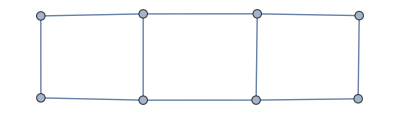
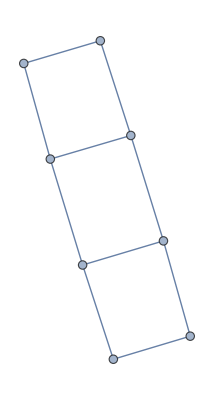

```mathematica
{IGLayoutFruchtermanReingold[IGMakeLattice[{2,4}](*, "Align" -> True is the default *)],IGLayoutFruchtermanReingold[IGMakeLattice[{2,4}],"Align"->False]}
```

"Continue" → True allows using existing vertex coordinates as starting points for algorithms that update vertex positions incrementally. We can use this to visualize how the layout algorithms work …

```mathematica
g=IGLayoutRandom@RandomGraph[BarabasiAlbertGraphDistribution[100,1]];
ListAnimate@NestList[IGLayoutGraphOpt[#,"Continue"->True,"MaxIterations"->80]&,g,40]
```

… or to visualize dynamic graph processes such as adding edges to the graph one by one:

```mathematica
g=IGLayoutKamadaKawai@Graph[Range[25],{1<->25},VertexLabels->"Name"];
ListAnimate@NestList[
IGLayoutKamadaKawai[EdgeAdd[#,UndirectedEdge@@RandomSample[VertexList[#],2]],"MaxIterations"->15,"Continue"->True,"Align"->False]&,
g,
30
]
```

### Drawing trees

IGLayoutRengoldTilford[] and IGLayoutRengoldTilfordCircular[] are designed for laying out trees. The following options are available:

"RootVertices" allows nodes to be used as the root nodes in the layout. It must be a list, even if there is a single root node. Multiple root nodes are meant to be used with forests.

DirectedEdges → True lays out the graph so that directed edges are pointing form lower levels (near the root) towards higher ones (away from the root).

"Rotation" controls the orientation of the layout. It must be given in radians.

### Drawing large graphs

IGLayoutDrL is designed specifically for large graphs with high clustering. The following image is created using DrL.

-Graphics-

The image was generated using the following code:

```mathematica
lg=ExampleData[{"NetworkGraph","CondensedMatterCollaborations2005"}];
lg=IndexGraph@Subgraph[lg,First@ConnectedComponents[lg]];
c=IGCommunitiesMultilevel[lg]
pts=GraphEmbedding@IGLayoutDrL[lg]; (* this takes a while *)
figure=Graphics[
GraphicsComplex[pts,
{
{White,AbsoluteThickness[0.3],Opacity[0.05],
Line[List@@@EdgeList[lg]]},
{AbsolutePointSize[2],Opacity[0.7],
MapIndexed[
{ColorData[45]@First[#2],Point[#1]}&,
c["Communities"]
]}
}
],
Background->Black
]
```

### Gallery

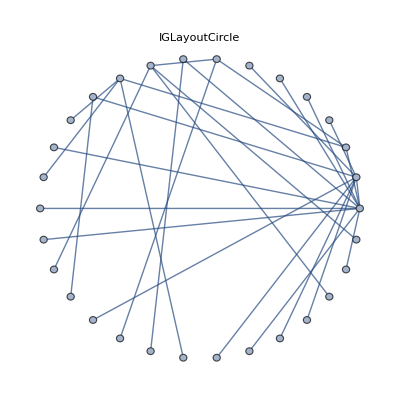
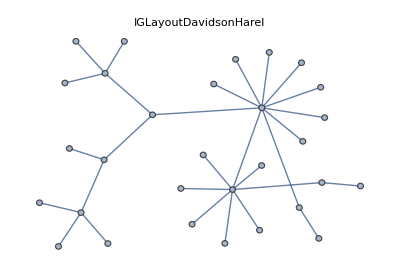
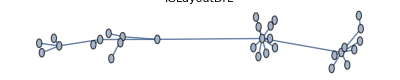
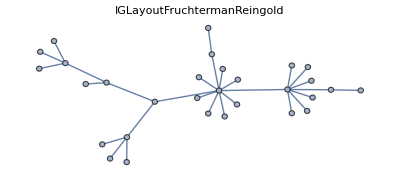
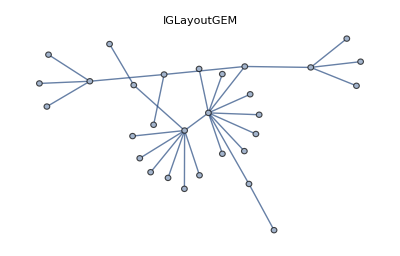
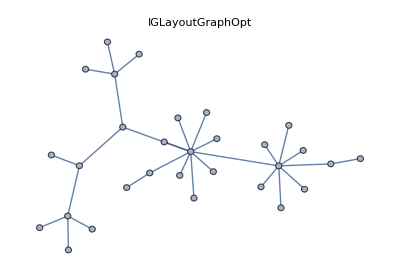
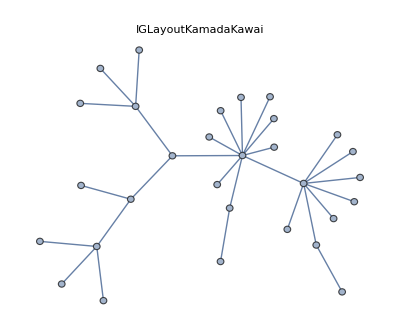
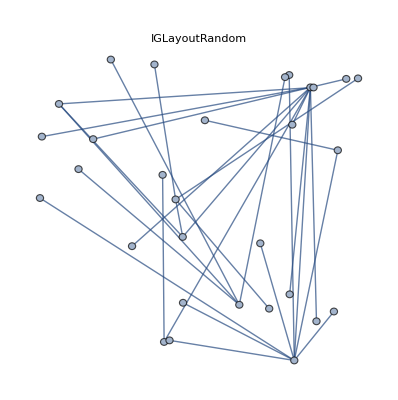
-Graphics- | -Graphics- | -Graphics- | -Graphics3D-
-Graphics- | -Graphics3D- | -Graphics- | -Graphics-
-Graphics- | -Graphics3D- | -Graphics- | -Graphics-
-Graphics- | -Graphics3D- |  |

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[30,1]];
layouts=Graph[#[g],PlotLabel->#]&/@{IGLayoutCircle,IGLayoutDavidsonHarel,IGLayoutDrL,IGLayoutDrL3D,IGLayoutFruchtermanReingold,IGLayoutFruchtermanReingold3D,IGLayoutGEM,IGLayoutGraphOpt,IGLayoutKamadaKawai,IGLayoutKamadaKawai3D,IGLayoutRandom,IGLayoutReingoldTilford,IGLayoutReingoldTilfordCircular,IGLayoutSphere};
Grid@Partition[layouts,4,4,{1,1},""]
```

## Community detection

The following functions are available:

```mathematica
?IGCommunities*
```

### Concepts

Modularity is defined for a given partitinoning of a graph’s vertices into communities. It is defined as Q=1/(2m)∑_(i,j) (A_(i,j)-(k_i k_j)/(2m))δ_(c_i c_j), where m is the number of edges, A is the adjacency matrix, k_i is the degree of node i, and c_i is the community that node i belongs to. δ_(i,j) is the Kronecker δ symbol. For weighted graphs, A is the weighted adjacency matrix, k_i are the sum of weights of edges incident on node i, and m is the sum of all weights.

IGModularity[graph,communities] is equivalent to GraphAssortativity[graph,communities,"Normalized"→Fase]

### Functions

#### IGCommunitiesEdgeBetweenness

IGCommunitiesEdgeBetweenness[] implements the Girvan–Newman algorithm.

It works on weighted graphs.

Reference:  M. Girvan and M. E. J. Newman: Community structure in social and biological networks, Proc. Nat. Acad. Sci. USA 99, 7821-7826 (2002).

#### IGCommunitiesGreedy

IGCommunitiesGreedy[] implements greedy optimization of modularity.

It works on weighted graphs.

Reference: A Clauset, MEJ Newman, C Moore: Finding community structure in very large networks, http://www.arxiv.org/abs/cond-mat/0408187

#### IGCommunitiesLabelPropagation

It supports weighted graphs.

Reference:  Raghavan, U.N. and Albert, R. and Kumara, S.: Near linear time algorithm to detect community structures in large-scale networks. Phys Rev E 76, 036106. (2007).

#### IGCommunitiesOptimalModularity

It supports weighted graphs.

#### IGCommunitiesLeadingEigenvector

It supports weighted graphs.

Reference: MEJ Newman: Finding community structure using the eigenvectors of matrices, Phys Rev E 74:036104 (2006).

#### IGCommunitiesSpinGlass

It supports weighted graphs.

Option values for "Method" are: "Original", "Negative"

Option values for "UpdateRule" are: "Simple", "Configuration"

References:

For Method→"Original, see Joerg Reichardt and Stefan Bornholdt: Statistical Mechanics of Community Detection, http://arxiv.org/abs/cond-mat/0603718

For Method→"Negative", see V.A. Traag and Jeroen Bruggeman: Community detection in networks with positive and negative links, http://arxiv.org/abs/0811.2329

#### IGCommunitiesInfoMAP

IGCommunitiesInfoMAP[] implements the InfoMAP algorithm.

It supports both edge weights and vertex weights.

The default number of trials is 10.

References:
M. Rosvall and C. T. Bergstrom, Maps of information flow reveal community structure in complex networks, PNAS 105, 1118 (2008) 
M. Rosvall, D. Axelsson, and C. T. Bergstrom, The map equation, Eur. Phys. J. Special Topics 178, 13 (2009)

#### IGCommunitiesMultilevel

IGCommunitiesMultilevel[] implements the Louvain community detection method.

It supports weighted graphs.

Reference: VD Blondel, J-L Guillaume, R Lambiotte and E Lefebvre: Fast unfolding of community hierarchies in large networks, J Stat Mech P10008 (2008)

#### IGCommunitiesWalktrap

IGCommunitiesWalktrap[] finds communities using short random walks, exploiting the fact that random walks tend to stay within the same cluster.

Is supports weighted graphs.

The default number of steps is 4.

Reference: Pascal Pons, Matthieu Latapy: Computing communities in large networks using random walks, http://arxiv.org/abs/physics/0512106

### Examples

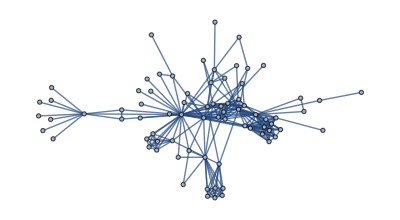

```mathematica
g=ExampleData[{"NetworkGraph","LesMiserables"}]
```

```mathematica
WeightedGraphQ[g]
```

True

Community detection functions return IGClusters objects.

```mathematica
cl1=IGCommunitiesEdgeBetweenness[g]
cl2=IGCommunitiesWalktrap[g]
```

IGClusterData[]

IGClusterData[]

Various properties of these objects can be queried:

```mathematica
cl1["Communities"]
```

{{Myriel,Napoleon,Mlle Baptistine,Mme. Magloire,Countess De Lo,Geborand,Champtercier,Cravatte,Count,Old Man},{Labarre,Valjean,Marguerite,Mme. De R,Isabeau,Gervais,Fauchelevent,Bamatabois,Perpetue,Simplice,Scaufflaire,Woman1,Judge,Champmathieu,Brevet,Chenildieu,Cochepaille,Mother Innocent,Gribier},{Tholomyes,Listolier,Fameuil,Blacheville,Favourite,Dahlia,Zephine,Fantine},{Mme. Thenardier,Thenardier,Cosette,Javert,Pontmercy,Boulatruelle,Eponine,Anzelma,Woman2,Gillenormand,Magnon,Mlle Gillenormand,Mme. Pontmercy,Mlle Vaubois,Lt. Gillenormand,Marius,Baroness T,Gueulemer,Babet,Claquesous,Montparnasse,Toussaint,Brujon},{Jondrette,Mme. Burgon,Gavroche,Mabeuf,Enjolras,Combeferre,Prouvaire,Feuilly,Courfeyrac,Bahorel,Bossuet,Joly,Grantaire,Mother Plutarch,Child1,Child2,Mme. Hucheloup}}

```mathematica
CommunityGraphPlot[g,cl1["Communities"]]
```

-Graphics-

The available properties depend on which algorithm was used for community detection. The following are always present:

"Algorithm" returns the algorithm used for community detection.

"Communities" returns the list of communities.

"Elements" returns the vertices of the graph.

"ElementCount" returns the vertex count of the graph.

"Properties" returns all available properties.

These are present for hierarchical clustering methods:

"HierarchicalClusters" returns the clustering in a format compatible with the Hierarchical Clustering standard package.

"Merges" represents the hierarchical clustering as a sequence of element merges. Elements are represented by their integer indices, and higher indices are introduced for the subclusters formed by the merges. This format is similar to the one used by MATLAB and many other tools.

"Tree" gives a binary tree representation of the merges.

Additionally, the following, and other, algorithm-specific properties may be present:

"Modularity" is a list of modularities for each step of the algorithm. What consitutes a step depends on the particular algorithm.

```mathematica
cl1["Properties"]
```

{Algorithm,Bridges,Communities,EdgeBetweenness,ElementCount,Elements,HierarchicalClusters,Merges,Modularity,Properties,RemovedEdges,Tree}

```mathematica
cl1["RemovedEdges"]
```

{Valjean<->Myriel,Valjean<->Mlle Baptistine,Valjean<->Mme. Magloire,Gavroche<->Valjean,Gavroche<->Javert,Thenardier<->Fantine,Bamatabois<->Javert,Bossuet<->Valjean,Montparnasse<->Valjean,Gueulemer<->Gavroche,Babet<->Gavroche,Claquesous<->Valjean,Gueulemer<->Valjean,Babet<->Valjean,Toussaint<->Valjean,Montparnasse<->Javert,Bamatabois<->Fantine,Gillenormand<->Valjean,Woman1<->Javert,Mlle Gillenormand<->Valjean,Woman2<->Valjean,Enjolras<->Valjean,Simplice<->Javert,Fantine<->Marguerite,Fauchelevent<->Javert,Simplice<->Fantine,Mme. Thenardier<->Valjean,Perpetue<->Fantine,Fantine<->Valjean,Thenardier<->Valjean,Javert<->Valjean,Marius<->Valjean,Cosette<->Valjean,Marius<->Tholomyes,Cosette<->Tholomyes,Mme. Thenardier<->Fantine,Javert<->Fantine,Gavroche<->Thenardier,Mabeuf<->Marius,Montparnasse<->Thenardier,Feuilly<->Marius,Bahorel<->Marius,Claquesous<->Javert,Joly<->Marius,Mabeuf<->Eponine,Claquesous<->Mme. Thenardier,Gueulemer<->Eponine,Montparnasse<->Gavroche,Brujon<->Gavroche,Courfeyrac<->Eponine,Claquesous<->Enjolras,Marius<->Gavroche,Enjolras<->Javert,Bossuet<->Marius,Combeferre<->Marius,Enjolras<->Marius,Courfeyrac<->Marius,Mother Innocent<->Valjean,Fauchelevent<->Valjean,Javert<->Cosette,Magnon<->Mme. Thenardier,Lt. Gillenormand<->Cosette,Pontmercy<->Thenardier,Marius<->Thenardier,Mlle Gillenormand<->Cosette,Gillenormand<->Cosette,Marius<->Eponine,Marius<->Cosette,Gavroche<->Mme. Burgon,Simplice<->Valjean,Woman2<->Javert,Cosette<->Thenardier,Toussaint<->Javert,Cosette<->Mme. Thenardier,Mabeuf<->Gavroche,Mme. Hucheloup<->Gavroche,Grantaire<->Gavroche,Prouvaire<->Gavroche,Feuilly<->Gavroche,Joly<->Gavroche,Bossuet<->Gavroche,Bahorel<->Gavroche,Combeferre<->Gavroche,Enjolras<->Gavroche,Courfeyrac<->Gavroche,Valjean<->Labarre,Marguerite<->Valjean,Mme. De R<->Valjean,Anzelma<->Mme. Thenardier,Babet<->Eponine,Eponine<->Mme. Thenardier,Montparnasse<->Eponine,Brujon<->Montparnasse,Mother Plutarch<->Mabeuf,Marius<->Pontmercy,Lt. Gillenormand<->Mlle Gillenormand,Marius<->Mlle Gillenormand,Mlle Gillenormand<->Gillenormand,Mme. Hucheloup<->Grantaire,Isabeau<->Valjean,Boulatruelle<->Thenardier,Brujon<->Eponine,Claquesous<->Eponine,Napoleon<->Myriel,Gervais<->Valjean,Mme. Hucheloup<->Bahorel,Feuilly<->Mabeuf,Grantaire<->Feuilly,Feuilly<->Prouvaire,Countess De Lo<->Myriel,Scaufflaire<->Valjean,Eponine<->Thenardier,Anzelma<->Thenardier,Grantaire<->Bahorel,Bahorel<->Mabeuf,Bahorel<->Prouvaire,Geborand<->Myriel,Woman1<->Valjean,Grantaire<->Combeferre,Joly<->Mabeuf,Mme. Hucheloup<->Joly,Bossuet<->Prouvaire,Mme. Hucheloup<->Courfeyrac,Enjolras<->Mabeuf,Bossuet<->Mabeuf,Grantaire<->Courfeyrac,Prouvaire<->Combeferre,Courfeyrac<->Prouvaire,Grantaire<->Joly,Joly<->Prouvaire,Combeferre<->Mabeuf,Courfeyrac<->Mabeuf,Grantaire<->Enjolras,Grantaire<->Bossuet,Prouvaire<->Enjolras,Champtercier<->Myriel,Mme. Hucheloup<->Enjolras,Bossuet<->Bahorel,Mme. Hucheloup<->Bossuet,Cravatte<->Myriel,Montparnasse<->Claquesous,Montparnasse<->Gueulemer,Montparnasse<->Babet,Count<->Myriel,Magnon<->Gillenormand,Mme. Pontmercy<->Mlle Gillenormand,Brujon<->Gueulemer,Babet<->Mme. Thenardier,Babet<->Javert,Claquesous<->Gueulemer,Brujon<->Thenardier,Babet<->Gueulemer,Claquesous<->Thenardier,Babet<->Thenardier,Old Man<->Myriel,Joly<->Courfeyrac,Bahorel<->Courfeyrac,Courfeyrac<->Feuilly,Courfeyrac<->Combeferre,Bossuet<->Courfeyrac,Courfeyrac<->Enjolras,Brevet<->Bamatabois,Chenildieu<->Bamatabois,Cochepaille<->Bamatabois,Bamatabois<->Valjean,Judge<->Bamatabois,Champmathieu<->Bamatabois,Woman2<->Cosette,Mother Innocent<->Fauchelevent,Lt. Gillenormand<->Gillenormand,Baroness T<->Marius,Marius<->Gillenormand,Bahorel<->Combeferre,Bahorel<->Feuilly,Joly<->Bahorel,Bahorel<->Enjolras,Joly<->Enjolras,Feuilly<->Enjolras,Bossuet<->Enjolras,Combeferre<->Enjolras,Javert<->Thenardier,Gueulemer<->Thenardier,Thenardier<->Mme. Thenardier,Brujon<->Babet,Claquesous<->Babet,Mlle Baptistine<->Myriel,Mme. Magloire<->Myriel,Mme. Magloire<->Mlle Baptistine,Listolier<->Tholomyes,Favourite<->Tholomyes,Zephine<->Tholomyes,Fantine<->Tholomyes,Fameuil<->Tholomyes,Dahlia<->Tholomyes,Blacheville<->Tholomyes,Fameuil<->Listolier,Favourite<->Listolier,Zephine<->Listolier,Fantine<->Listolier,Dahlia<->Listolier,Blacheville<->Listolier,Blacheville<->Fameuil,Dahlia<->Fameuil,Zephine<->Fameuil,Fantine<->Fameuil,Favourite<->Fameuil,Favourite<->Blacheville,Zephine<->Blacheville,Fantine<->Blacheville,Dahlia<->Blacheville,Dahlia<->Favourite,Zephine<->Favourite,Fantine<->Favourite,Zephine<->Dahlia,Fantine<->Dahlia,Fantine<->Zephine,Javert<->Mme. Thenardier,Gueulemer<->Mme. Thenardier,Simplice<->Perpetue,Judge<->Valjean,Brevet<->Judge,Chenildieu<->Judge,Cochepaille<->Judge,Champmathieu<->Judge,Champmathieu<->Valjean,Brevet<->Champmathieu,Chenildieu<->Champmathieu,Cochepaille<->Champmathieu,Brevet<->Valjean,Chenildieu<->Brevet,Cochepaille<->Brevet,Chenildieu<->Valjean,Cochepaille<->Chenildieu,Cochepaille<->Valjean,Anzelma<->Eponine,Gribier<->Fauchelevent,Mme. Burgon<->Jondrette,Mme. Pontmercy<->Pontmercy,Mlle Vaubois<->Mlle Gillenormand,Marius<->Lt. Gillenormand,Baroness T<->Gillenormand,Feuilly<->Combeferre,Joly<->Feuilly,Bossuet<->Feuilly,Bossuet<->Combeferre,Joly<->Bossuet,Joly<->Combeferre,Grantaire<->Prouvaire,Gueulemer<->Javert,Toussaint<->Cosette,Child1<->Gavroche,Child2<->Gavroche,Child2<->Child1,Brujon<->Claquesous}

```mathematica
cl2["Properties"]
```

{Algorithm,Communities,ElementCount,Elements,HierarchicalClusters,Merges,Modularity,Properties,Tree}

```mathematica
IGCompareCommunities[cl1,cl2]
```

<|VariationOfInformation→0.903678,NormalizedMutualInformation→0.739339,SplitJoinDistance→35,UnadjustedRandIndex→0.844839,AdjustedRandIndex→0.500085|>

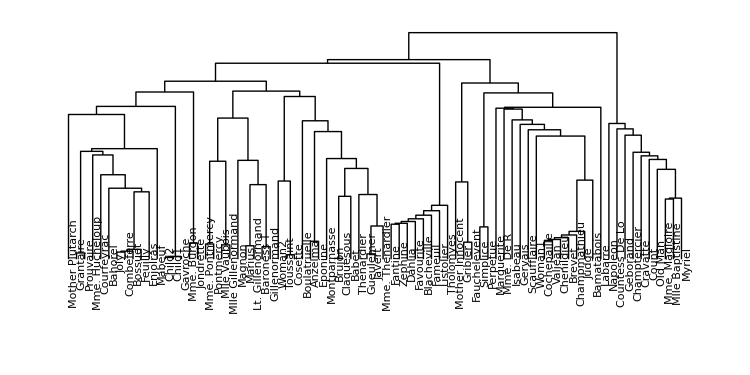

```mathematica
DendrogramPlot[cl1["HierarchicalClusters"],LeafLabels->(Rotate[#,Pi/2]&),ImageSize->750,AspectRatio->1/2]
```

## Notes on other functions

### Random number generator

igraph’s random number generator can be seeded using

```mathematica
IGSeedRandom[123]
```

### IGData[]

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order motif counting functions use.

```mathematica
IGData[]
```

{{AllDirectedGraphs,3},{AllDirectedGraphs,4},MANTriadLabels}

Here’s all size 3 directed graphs.

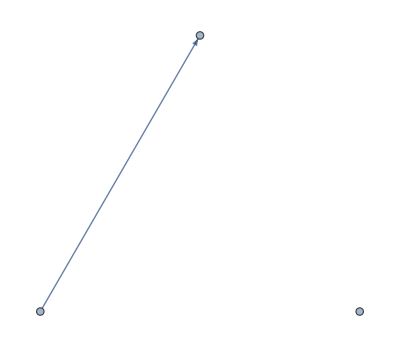
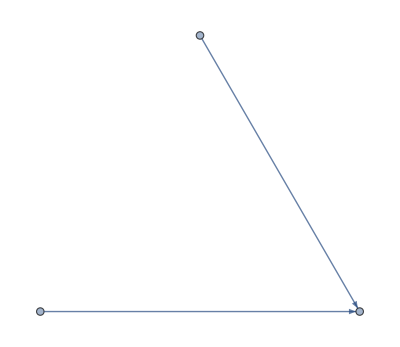
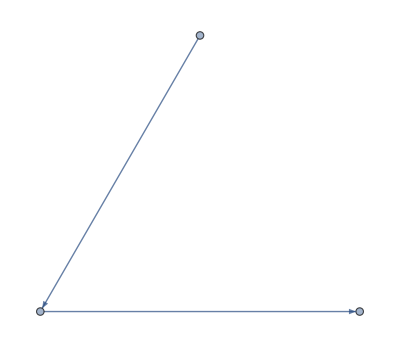
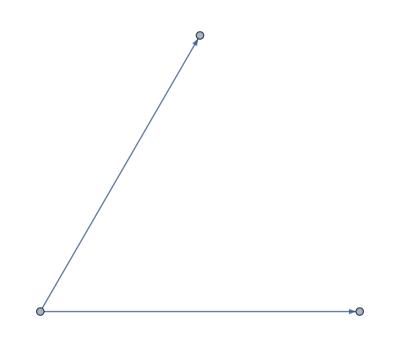
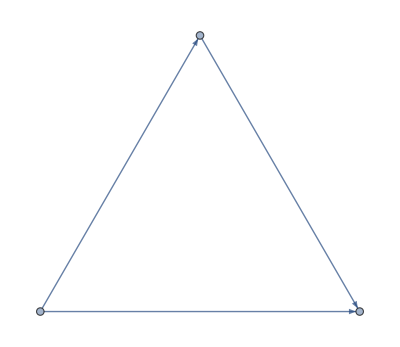
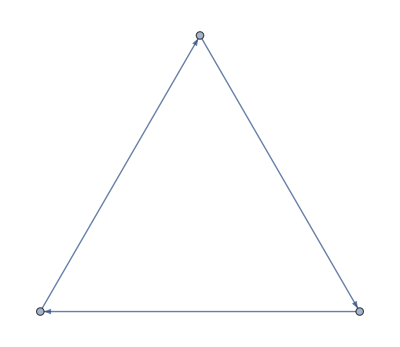
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@IGData[{"AllDirectedGraphs",3}]
```

"MANTriadLabels" refers to the mutual, asymmetric, null labelling of triads used by IGTriadCensus[]. Each label is mapped to the corresponding graph, ordered based on their IGIsoclass. This is useful for converting the output of IGTriadCensus[] to a format compatible with IGMotifs[].